# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
sims = SemanticImport[FileNameJoin[{NotebookDirectory[],"MH_data.txt"}]];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
clist = sims[All,#c&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport[FileNameJoin[{NotebookDirectory[],"CDF_data.txt"}]];
```

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,250^α/2];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,250^α/2];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,250^α/2];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(2/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(2*Pi(Dα/μ)^(2/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,250^α/2];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

(α-1)+O[α-1]^2

```mathematica
xlist=10^Range[-14,8.5,.25];
```

```mathematica
xlist
```

{1.×10^-14,1.77828×10^-14,3.16228×10^-14,5.62341×10^-14,1.×10^-13,1.77828×10^-13,3.16228×10^-13,5.62341×10^-13,1.×10^-12,1.77828×10^-12,3.16228×10^-12,5.62341×10^-12,1.×10^-11,1.77828×10^-11,3.16228×10^-11,5.62341×10^-11,1.×10^-10,1.77828×10^-10,3.16228×10^-10,5.62341×10^-10,1.×10^-9,1.77828×10^-9,3.16228×10^-9,5.62341×10^-9,1.×10^-8,1.77828×10^-8,3.16228×10^-8,5.62341×10^-8,1.×10^-7,1.77828×10^-7,3.16228×10^-7,5.62341×10^-7,1.×10^-6,1.77828×10^-6,3.16228×10^-6,5.62341×10^-6,0.00001,0.0000177828,0.0000316228,0.0000562341,0.0001,0.000177828,0.000316228,0.000562341,0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28,5623.41,10000.,17782.8,31622.8,56234.1,100000.,177828.,316228.,562341.,1.×10^6,1.77828×10^6,3.16228×10^6,5.62341×10^6,1.×10^7,1.77828×10^7,3.16228×10^7,5.62341×10^7,1.×10^8,1.77828×10^8,3.16228×10^8}

```mathematica
αlistnew = {.3,.5}
```

{0.3,0.5}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(k*BesselJ[0,k x]*Exp[-10^-12*k^2])/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlistnew[[;;]]}]];
```

```mathematica
xmaxes=AssociationThread[αlistnew,{100000,100000}];
```

# Plots

## α=0.5

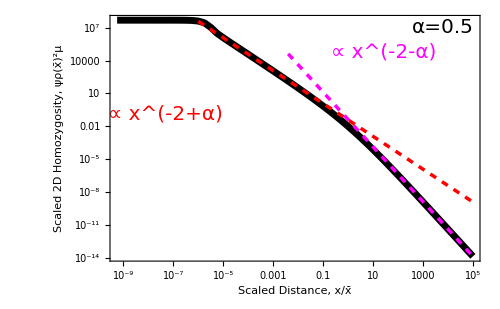

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦1;;4⟧},
Show[ListLogLogPlot[Table[{x,(4*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-12,100000},{10^-15,10^9}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.004,100000},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.000001,100000},PlotStyle->{Red,Dashed,Thickness[.005]}],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled 2D Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=0.3

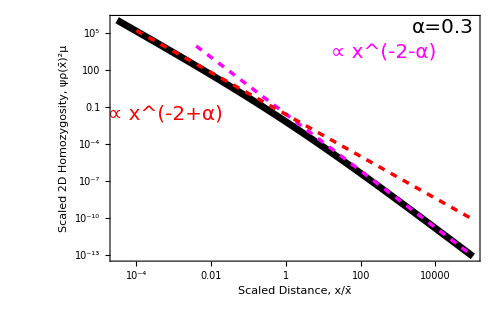

```mathematica
Module[{α=0.3,coal =.01, plotpoints,μvals=μlist⟦1;;4⟧},
Show[ListLogLogPlot[Table[{x,(4*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-10,100000},{10^-15,10^6}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.004,100000},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.0001,100000},PlotStyle->{Red,Dashed,Thickness[.005]}],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=0.3",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled 2D Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

# 2D Asymptotics

```mathematica
(*These are expressions for ψ(x)/(1-ψ(0)) *)
```

## x << δ

```mathematica
(4*Pi*ρ*D)^-1*Integrate[k*Exp[-k^2*delta^2/2]/( k^a),{k,0,Infinity}, Assumptions->{x > 0, delta > 0, a > 0}]
```

ConditionalExpression[(2^(-2-a/2) delta^(-2+a) Gamma[1-a/2])/(D π ρ),a<2]

## δ << x << x̄

```mathematica
(4*Pi*ρ*D)^-1*InverseHankelTransform[
Abs[k]^(-a),k,x]
```

(2^(-1-a) x^(-2+a) Gamma[1-a/2])/(D π ρ Gamma[a/2])

## x >> x̄

```mathematica
(4*Pi*ρ*mu*xbar^2)^-1*xbar^(a+2)*InverseHankelTransform[
Abs[k]^(a),k,x]
```

(2^(-1+a) x^(-2-a) xbar^a Gamma[1+a/2])/(mu π ρ Gamma[-a/2])

```mathematica
(*Note that xbar = (D/mu)^(1/a)*)
```